# UpSetChart Tests

```mathematica
Quit[];
```

```mathematica
$Path=Prepend[$Path,NotebookDirectory[]];
<<UpSetChart`
```

```mathematica
<<UpSetChart`TestData`
sets=DummyData[3]
```

<|Red→{Strawberry,Apple},Green→{Kiwi,Pear,Cucumber,Pickle},Tasty→{Kiwi,Pear},Fruit→{Kiwi,Lemon,Banana,Strawberry,Pear,Apple,Carrot},Vegetable→{Cucumber,Pickle}|>

```mathematica
DynamicUpSetChart[sets,"TabbedByComparisonsDegreeQ"->True,"ImageSize"->{Automatic,100}]
```

```mathematica
UpSetChart`UpSetChart
```

UpSetChart

## The Packages of UpSetChart

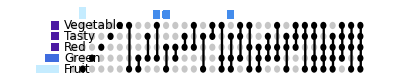

```mathematica
UpSetChart[sets,"DropEmpty"->False]
```

## Unique Intersections

```mathematica
(* Calculates the unique elements for the comparisons *)
<<UpSetChart`UniqueIntersections`
```

```mathematica
UniqueIntersections[sets]
```

<|sets→<|Red→{Strawberry,Apple},Green→{Kiwi,Pear,Cucumber,Pickle},Tasty→{Kiwi,Pear},Fruit→{Kiwi,Lemon,Banana,Strawberry,Pear,Apple,Carrot},Vegetable→{Cucumber,Pickle}|>,setNames→{Red,Green,Tasty,Fruit,Vegetable},comparisons→{{},{Red},{Green},{Tasty},{Fruit},{Vegetable},{Red,Green},{Red,Tasty},{Red,Fruit},{Red,Vegetable},{Green,Tasty},{Green,Fruit},{Green,Vegetable},{Tasty,Fruit},{Tasty,Vegetable},{Fruit,Vegetable},{Red,Green,Tasty},{Red,Green,Fruit},{Red,Green,Vegetable},{Red,Tasty,Fruit},{Red,Tasty,Vegetable},{Red,Fruit,Vegetable},{Green,Tasty,Fruit},{Green,Tasty,Vegetable},{Green,Fruit,Vegetable},{Tasty,Fruit,Vegetable},{Red,Green,Tasty,Fruit},{Red,Green,Tasty,Vegetable},{Red,Green,Fruit,Vegetable},{Red,Tasty,Fruit,Vegetable},{Green,Tasty,Fruit,Vegetable},{Red,Green,Tasty,Fruit,Vegetable}},numberOfSets→5,elementsUniqueToComparisons→<|{}→{},{Red,Green,Tasty,Fruit,Vegetable}→{},{Red,Green,Tasty,Fruit}→{},{Red,Green,Tasty,Vegetable}→{},{Red,Green,Fruit,Vegetable}→{},{Red,Tasty,Fruit,Vegetable}→{},{Green,Tasty,Fruit,Vegetable}→{},{Red,Green,Tasty}→{},{Red,Green,Fruit}→{},{Red,Green,Vegetable}→{},{Red,Tasty,Fruit}→{},{Red,Tasty,Vegetable}→{},{Red,Fruit,Vegetable}→{},{Green,Tasty,Fruit}→{Kiwi,Pear},{Green,Tasty,Vegetable}→{},{Green,Fruit,Vegetable}→{},{Tasty,Fruit,Vegetable}→{},{Red,Green}→{},{Red,Tasty}→{},{Red,Fruit}→{Apple,Strawberry},{Red,Vegetable}→{},{Green,Tasty}→{},{Green,Fruit}→{},{Green,Vegetable}→{Cucumber,Pickle},{Tasty,Fruit}→{},{Tasty,Vegetable}→{},{Fruit,Vegetable}→{},{Red}→{},{Green}→{},{Tasty}→{},{Fruit}→{Banana,Carrot,Lemon},{Vegetable}→{}|>|>

## Utilities

Utilities contains several conditional checkers and helpers.

```mathematica
(* Conditionals for types & passing down options *)
<<UpSetChart`Utilities`
```

```mathematica
EnsureLabeledSets[{{1,2,3},{2,3,4,4,4}}]
```

<|a→{1,2,3},b→{2,3,4}|>

```mathematica
sets={{1,2,3},{2,3,4,4,4}};
ListOfListsQ[sets]
LabeledSetsQ[sets]
LabeledSetsQ[EnsureLabeledSets[sets]]
```

True

False

True

## Calculations

While Unique Intersections does all the calculations we need for this chart, the chart may want us to sort and filter results as well.
This “super” function does this.

```mathematica
(* Calls UniqueIntersections and sorts & filters data *)
<<UpSetChart`Calculations`
```

```mathematica
calc=CalcThenSortAndFilter[sets]
```

<|sets→<|Fruit→{Kiwi,Lemon,Banana,Strawberry,Pear,Apple,Carrot},Green→{Kiwi,Pear,Cucumber,Pickle},Red→{Strawberry,Apple},Tasty→{Kiwi,Pear},Vegetable→{Cucumber,Pickle}|>,comparisons→<|{Fruit}→{Banana,Carrot,Lemon},{Green,Vegetable}→{Cucumber,Pickle},{Red,Fruit}→{Apple,Strawberry},{Green,Tasty,Fruit}→{Kiwi,Pear}|>|>

### Calculation Utilities

```mathematica
(* Sort & filter functions *)
<<UpSetChart`Calculations`Utilities`
```

## Graphics

```mathematica
(* Returns the graphics for UpSetChart *)
<<UpSetChart`Graphics`
```

Graphics is a wrapper GraphicComponents returning the Graphic Item. Allows for processing of the Options before passing them

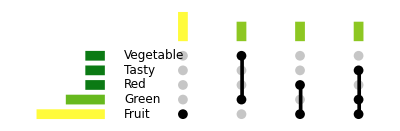

```mathematica
UpSetGraphics[
	calc["sets"], 
	calc["comparisons"],
	"ColorGradient"->"AvocadoColors",
	"ComponentSpacing"->{1,1},
	"IndicatorRadius"->0.5,
	"IndicatorSpacing"->{5,1/2}
]
```

### Utilities

Graphic Utilities is a wrapper over the four main components and returns them as a list.

```mathematica
(* Returns each components for the UpSetChart *)
<<UpSetChart`Graphics`Utilities`
```

```mathematica
gc=GraphicComponents[calc["sets"], calc["comparisons"],"IndicatorRadius"->1];
```

{Translate[{{RGBColor[0.772061, 0.92462, 0.998703],Rectangle[{0,2},{7,4}]},{RGBColor[0.24882928571428573, 0.42314085714285715, 0.8732312857142858],Rectangle[{3,5},{7,7}]},{RGBColor[0.29575928571428567, 0.09888902857142857, 0.634997],Rectangle[{5,8},{7,10}]},{RGBColor[0.29575928571428567, 0.09888902857142857, 0.634997],Rectangle[{5,11},{7,13}]},{RGBColor[0.29575928571428567, 0.09888902857142857, 0.634997],Rectangle[{5,14},{7,16}]}},{0,0}],Translate[{{RGBColor[0.772061, 0.92462, 0.998703],Rectangle[Offset[{54,0},{2,0}],Offset[{54,0},{4,3}]]},{RGBColor[0.26669366666666666, 0.550462, 0.926485],Rectangle[Offset[{54,0},{5,0}],Offset[{54,0},{7,2}]]},{RGBColor[0.26669366666666666, 0.550462, 0.926485],Rectangle[Offset[{54,0},{8,0}],Offset[{54,0},{10,2}]]},{RGBColor[0.26669366666666666, 0.550462, 0.926485],Rectangle[Offset[{54,0},{11,0}],Offset[{54,0},{13,2}]]}},{9,17}],Translate[{Text[Fruit,{0,3},{-1,0}],Text[Green,{0,6},{-1,0}],Text[Red,{0,9},{-1,0}],Text[Tasty,{0,12},{-1,0}],Text[Vegetable,{0,15},{-1,0}]},{9,0}],Translate[{{{{GrayLevel[0],Disk[Offset[{54,0},{3,3}],1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[Offset[{54,0},{6,3}],1]},{GrayLevel[0],Disk[Offset[{54,0},{9,3}],1]},{GrayLevel[0],Disk[Offset[{54,0},{12,3}],1]}},{{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[Offset[{54,0},{3,6}],1]},{GrayLevel[0],Disk[Offset[{54,0},{6,6}],1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[Offset[{54,0},{9,6}],1]},{GrayLevel[0],Disk[Offset[{54,0},{12,6}],1]}},{{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[Offset[{54,0},{3,9}],1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[Offset[{54,0},{6,9}],1]},{GrayLevel[0],Disk[Offset[{54,0},{9,9}],1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[Offset[{54,0},{12,9}],1]}},{{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[Offset[{54,0},{3,12}],1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[Offset[{54,0},{6,12}],1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[Offset[{54,0},{9,12}],1]},{GrayLevel[0],Disk[Offset[{54,0},{12,12}],1]}},{{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[Offset[{54,0},{3,15}],1]},{GrayLevel[0],Disk[Offset[{54,0},{6,15}],1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[Offset[{54,0},{9,15}],1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[Offset[{54,0},{12,15}],1]}}},{{GrayLevel[0],Rectangle[Offset[{54,0},{11/4,3}],Offset[{54,0},{7/2,3}]]},{GrayLevel[0],Rectangle[Offset[{54,0},{23/4,6}],Offset[{54,0},{13/2,15}]]},{GrayLevel[0],Rectangle[Offset[{54,0},{35/4,3}],Offset[{54,0},{19/2,9}]]},{GrayLevel[0],Rectangle[Offset[{54,0},{47/4,3}],Offset[{54,0},{25/2,12}]]}}},{9,0}]}

### Comparisons Bar Chart

Comparisons Bar Chart produces the bar chart for the cardinality of the set comparisons

```mathematica
(* Components for charts *)
<<UpSetChart`Graphics`ComparisonsBarChart`
```

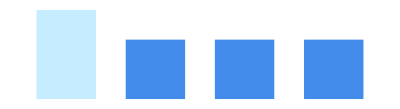

```mathematica
ComparisonsBarChart[calc["comparisons"],
 Max[Length/@calc["comparisons"]], Keys@calc["sets"]
]//Graphics[#,ImageSize->Tiny]&
```

### Grid Indicator

Grid Indicator produces the bubble heatmap which indicates which sets correspond to which comparisons

```mathematica
<<UpSetChart`Graphics`IndicatorGrid`
```

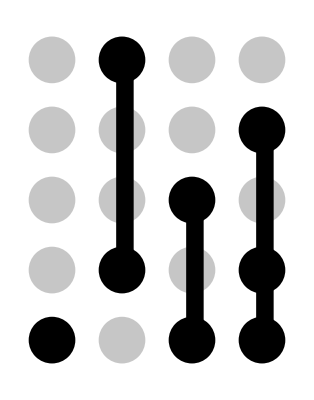

```mathematica
IndicatorGrid[Keys[calc["sets"]],Keys[calc["comparisons"]]]//Graphics[#,ImageSize->Tiny]&
```

### Sets Bar Chart

Produces the Bar Chart for the cardinality of sets

```mathematica
<<UpSetChart`Graphics`SetsBarChart`
```

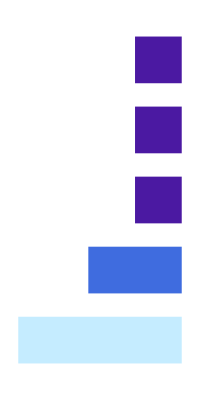

```mathematica
SetsBarChart[calc["sets"], Keys[calc["sets"]], Max[Length/@calc["sets"]]]//Graphics[#,ImageSize->Tiny]&
```

### Labels

Produces the labels of the sets. Works best with short labels

```mathematica
<<UpSetChart`Graphics`SetsLabels`
```

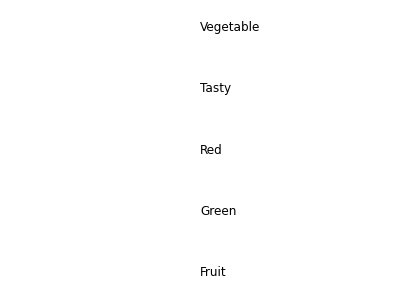

```mathematica
SetsLabels[ Keys[calc["sets"]]]//Graphics[#,ImageSize->Tiny]&
```